# MathPRINSAS

## Basic Architecture of Program

Link to one note: http://tiny.cc/7wkvbz

## XLS Format

### Here is online converter from Access 97 MDB to XLS: https://www.mdbopener.com/

## GUI

## IMPORT/EXPORT DIALOGS

```mathematica
OpenDB[curDir_:$HomeDirectory]:=SystemDialogInput[
"FileOpen",
{
curDir,
{"excel 2000"->{"*.xls"},"mdb"->{"*.mdb"},"accdb"->{"*.accdb"}}
},
WindowTitle->"Import DataBase"];


SaveDB[fileName_,curDir_:$HomeDirectory] := SystemDialogInput[
"FileSave",
{
FileNameJoin[{curDir,fileName}],
{"excel 2000"->{"*.xls"}}
},
WindowTitle->"Export DataBase"];


getDBFromFile[filePath_]:=Module[
{
sheetsNames = Import[filePath,"Sheets"],
db=Import[filePath]
},
(*record file path and its name*)
Association@MapThread[ToString[#1]->#2&,{sheetsNames,db}]
];
```

## DATA RECONFIGURATION

```mathematica
sansDB=parseDBToAssoc@getDBFromFile[OpenDB[]];
usansDB=parseDBToAssoc@getDBFromFile[OpenDB[]];
```

### DataFileInfo parsing

```mathematica
parseDBToAssoc[db_]:=Module[
{
dataFileInfoTitles = Rest[First[db["DataFileInfo"]]],
dataMeasurmentTitles = Rest[First[db["DataMeasurements"]]],
fileNamesList = Rest[db["DataFileInfo"]][[All,1]],
dataFileInfoWithoutFirstRowAndColumn=db["DataFileInfo"][[2;;-1,2;;-1]],
dbinfoAssoc=Association@MapIndexed[#1->First@Flatten@Rest[db["DBInfo"]][[All,#2]]&,db["DBInfo"][[1]]],
getMeasurmentsAssoc,
filesAssoc
},
getMeasurmentsAssoc[fileName_]:=Association@MapIndexed[
dataMeasurmentTitles[[First[#2]]]->#1&,
Transpose[Select[
db["DataMeasurements"],
First[#]===fileName&][[2;;-1,2;;-1]]
]
];
filesAssoc = 
Association@MapIndexed[
fileNamesList[[First[#2]]]->Association[{
"DataFileInfo"->Association@MapIndexed[(dataFileInfoTitles[[First[#2]]]->#1)&,#1],
"DataMeasurements"->getMeasurmentsAssoc[fileNamesList[[First[#2]]]]
}]&,
dataFileInfoWithoutFirstRowAndColumn
];
Association["files"->filesAssoc,"DBInfo"->dbinfoAssoc]
]
```

## FIT SANS AND USANS DEVELOPMENT

```mathematica
sansData=sansDB["files","N00001","DataMeasurements"];
usansData=usansDB["files","UN00001","DataMeasurements"];
```

```mathematica
sansData//Keys
usansData//Keys
```

{Q,I(Q),Masked,dI(Q)}

{Theta (arc sec),Timer,Monitor,Masked,I(Q),dI(Q)}

```mathematica
sansData["Q"]
```

{2.56699999e-03,2.90900003e-03,3.25100007e-03,3.59299988e-03,3.93600017e-03,4.27799998e-03,4.61999979e-03,4.96200006e-03,5.30399987e-03,5.64699993e-03,5.98900020e-03,6.33100001e-03,6.67299982e-03,7.01500010e-03,7.35800015e-03,7.69999996e-03,8.04200023e-03,8.38399958e-03,8.72599985e-03,9.06900037e-03,9.41099972e-03,9.75299999e-03,1.00999996e-02,1.04400003e-02,1.07800001e-02,1.11199999e-02,1.14599997e-02,1.18100001e-02,1.21499998e-02,1.24899996e-02,1.28300004e-02,1.31700002e-02,1.35199996e-02,1.38600003e-02,1.42000001e-02,1.45399999e-02,1.48900002e-02,1.52300000e-02,1.55699998e-02,1.59099996e-02,1.62499994e-02,1.65999997e-02,1.69399995e-02,1.72799993e-02,1.76199991e-02,1.79600008e-02,1.83099993e-02,1.86500009e-02,1.89900007e-02,1.93300005e-02,1.96800008e-02,2.00200006e-02,2.03600004e-02,2.07000002e-02,2.10400000e-02,2.13900004e-02,2.17300002e-02,2.20699999e-02,2.24099997e-02,2.27499995e-02,2.30999999e-02,2.34399997e-02,2.37799995e-02,2.41199993e-02,2.44600009e-02,2.48099994e-02,2.51499992e-02,2.54900008e-02,2.58300006e-02,2.61700004e-02,2.65200008e-02,2.68600006e-02,2.72000004e-02,2.75400002e-02,2.78800000e-02,2.80399993e-02,2.82300003e-02,2.85700001e-02,2.89099999e-02,2.92499997e-02,2.95899995e-02,2.99399998e-02,3.02799996e-02,3.06199994e-02,3.09599992e-02,3.13000008e-02,3.16400006e-02,3.17800008e-02,3.19899991e-02,3.23299989e-02,3.26699987e-02,3.30099985e-02,3.33499983e-02,3.37000005e-02,3.40400003e-02,3.43800001e-02,3.47199999e-02,3.50599997e-02,3.53999995e-02,3.55199985e-02,3.57500017e-02,3.60900015e-02,3.64300013e-02,3.67700011e-02,3.71100008e-02,3.74599993e-02,3.77999991e-02,3.81399989e-02,3.84799987e-02,3.88199985e-02,3.91599983e-02,3.92500013e-02,3.95100005e-02,3.98500003e-02,4.01900001e-02,4.29800004e-02,4.67200018e-02,5.04500009e-02,5.41800000e-02,5.79000004e-02,6.16299994e-02,6.53600022e-02,6.90800026e-02,7.28000030e-02,7.65200034e-02,8.02299976e-02,8.39499980e-02,8.76599997e-02,9.13700014e-02,9.50800031e-02,9.87799987e-02,1.02499999e-01,1.06200002e-01,1.09899998e-01,1.13600001e-01,1.17299996e-01,1.20899998e-01,1.24600001e-01,1.28299996e-01,1.31999999e-01,1.35700002e-01,1.39300004e-01,1.43000007e-01,1.46599993e-01,1.50299996e-01,1.53999999e-01,1.57600001e-01,1.61200002e-01,1.64900005e-01,1.68500006e-01,1.72099993e-01,1.75799996e-01,1.79399997e-01,1.82999998e-01,1.86600000e-01,1.90200001e-01,1.93800002e-01,1.97400004e-01,2.01000005e-01,2.04600006e-01,2.08199993e-01,2.11700007e-01,2.15299994e-01,2.18899995e-01,2.22399995e-01,2.25999996e-01,2.29499996e-01,2.33099997e-01,2.36599997e-01,2.40099996e-01,2.43599996e-01,2.47199997e-01,2.50699997e-01,2.54200011e-01,2.57699996e-01,2.61099994e-01,2.64600009e-01,2.68099993e-01,2.71600008e-01,2.75000006e-01,2.78499991e-01,2.81899989e-01,2.85400003e-01,2.88800001e-01,2.92199999e-01,2.95599997e-01,2.98999995e-01,3.02399993e-01,3.05799991e-01,3.09199989e-01,3.12599987e-01,3.16000015e-01,3.19299996e-01,3.22699994e-01,3.26000005e-01,3.29400003e-01,3.32700014e-01,3.35999995e-01,3.39399993e-01,3.42700005e-01,3.45999986e-01,3.49299997e-01,3.52499992e-01,3.55800003e-01,3.59100014e-01,3.62399995e-01,3.65599990e-01,3.68800014e-01,3.72099996e-01,3.75299990e-01,3.78500015e-01,3.81700009e-01,3.84900004e-01,3.88099998e-01,3.91299993e-01,3.94499987e-01,3.97700012e-01,4.00799990e-01,4.04000014e-01,4.07099992e-01,4.10200000e-01,4.13399994e-01,4.16500002e-01,4.19600010e-01,4.22699988e-01,4.25799996e-01,4.28799987e-01,4.31899995e-01,4.35000002e-01,4.37999994e-01}

```mathematica
Read[StringToStream[#],Number]&/@sansData["I(Q)"]
```

{1872.,1270.,913.9,689.3,537.6,433.3,366.8,304.2,258.7,224.1,198.9,167.6,153.1,135.2,127.8,113.9,100.8,93.8,86.01,80.22,75.04,70.84,63.69,59.34,55.06,51.81,49.08,45.47,42.97,40.57,40.01,37.14,35.15,35.09,32.09,31.33,30.31,28.91,27.22,27.85,25.84,24.69,23.94,22.76,20.96,22.18,20.22,20.46,20.16,19.,18.97,19.12,17.72,17.8,16.1,16.51,15.78,15.43,14.33,15.42,15.24,13.85,13.51,12.46,13.9,13.57,12.65,11.81,11.79,12.26,11.26,12.5,11.29,10.24,9.688,10.31,10.62,9.52,9.623,9.875,8.977,8.492,9.707,8.523,8.798,8.28,7.922,8.33,7.874,7.724,7.229,7.145,6.857,6.421,6.27,7.203,7.141,6.397,6.494,6.518,6.671,6.567,5.794,6.019,6.073,5.35,5.767,4.468,4.805,5.147,5.592,5.104,4.973,3.876,4.251,3.992,3.209,2.588,2.128,1.791,1.526,1.343,1.19,1.079,0.9797,0.9053,0.8602,0.8081,0.7831,0.745,0.7229,0.7045,0.6822,0.6756,0.6626,0.6471,0.6409,0.6313,0.628,0.6147,0.6156,0.6094,0.6003,0.5985,0.5946,0.5994,0.5975,0.5919,0.5874,0.5856,0.5757,0.5786,0.5732,0.5715,0.5697,0.5521,0.5454,0.5396,0.5262,0.5228,0.5216,0.5054,0.4865,0.4795,0.4684,0.4562,0.45,0.4314,0.4262,0.4108,0.3972,0.3879,0.3743,0.3601,0.3407,0.3267,0.3184,0.3022,0.2921,0.2738,0.265,0.2545,0.2389,0.2234,0.2131,0.2065,0.189,0.1791,0.1666,0.1521,0.1457,0.1332,0.125,0.1171,0.107,0.101,0.09963,0.08829,0.08526,0.08497,0.07779,0.07642,0.07121,0.06772,0.06476,0.06458,0.06391,0.06201,0.06116,0.05779,0.05971,0.05684,0.05564,0.05407,0.05521,0.05268,0.05186,0.05236,0.05007,0.05061,0.04671,0.05035,0.04478,0.04739,0.04754,0.04356,0.0458,0.04875,0.04257,0.04238}

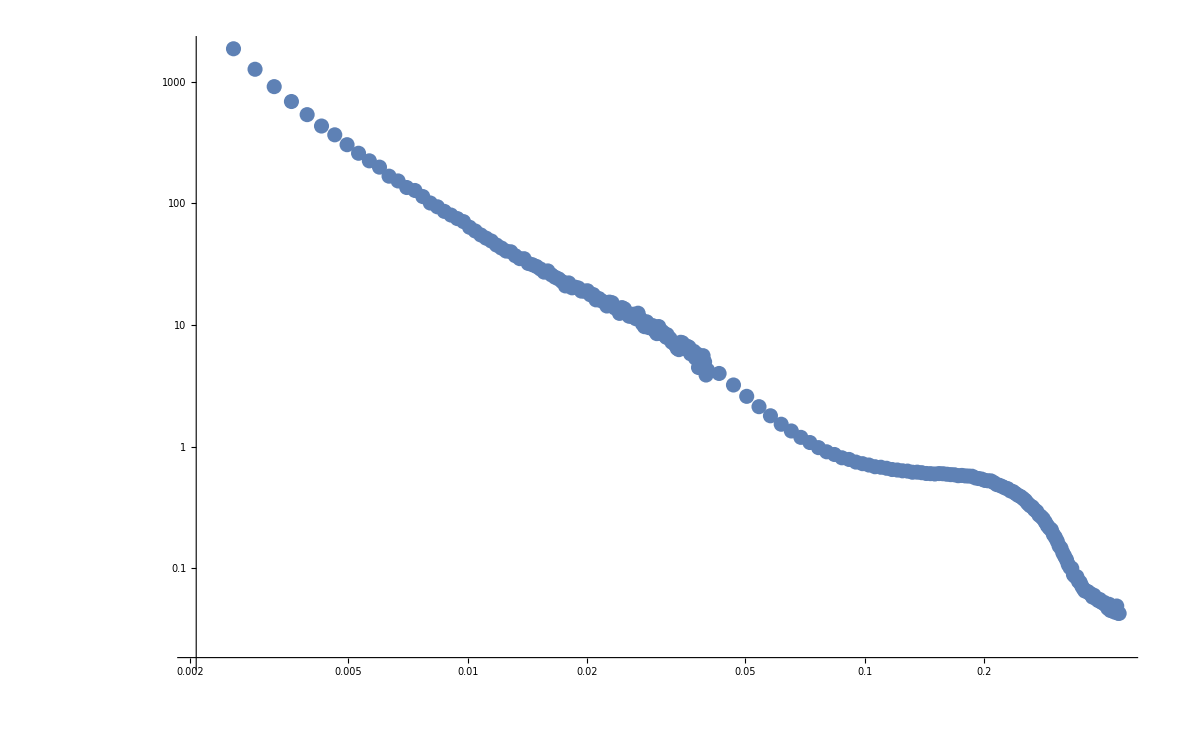

```mathematica
ListLogLogPlot[Transpose@{Read[StringToStream[#],Number]&/@sansData["Q"],Read[StringToStream[#],Number]&/@sansData["I(Q)"]}]
```

```mathematica
FitSANSandUSANS[sansData_,usansData_]:=Manipulate[ListLogLogPlot[{1,2,3,4,5}],{a,1,10}]
```

## MAIN GUI INTERFACE

```mathematica
MainGUI[curDirrectory_]:=
CreateDialog[
Panel[
DynamicModule[
{
fileList={},
DBStructure=Association[],
selectedDB={},
selectedFile={},
selectedSANS,
selectedUSANS,
newFilename="newFileName",

(*Inner functionality*)
AddDB,

(*CallBacks and Windows*)
DisplayXLS,
OnImport,
OnEdit,
OnClear,
OnSaveAs,
OnRemoveItems,
OnCreateNew,
OnFitPressed
},


OnClear[]:=(
fileList={};
DBStructure=Association[];
selectedDB={});


AddDB[filePath_]:=Module[
{
fileName=FileBaseName[filePath],
dbAssoc=parseDBToAssoc[getDBFromFile[filePath]]
},
(*record file path and its name*)

DBStructure[fileName]=Association["path"->filePath];
DBStructure[fileName]["db"]=dbAssoc
];


OnImport[]:=Module[
{
importedFiles
},
importedFiles=OpenDB[curDirrectory];
If[Not[importedFiles===$Canceled],
If[ListQ[importedFiles],
AddDB/@importedFiles;
fileList=Union[fileList, FileBaseName/@importedFiles];
,
AddDB[importedFiles];
AppendTo[fileList,FileBaseName[importedFiles]];
];
selectedDB={First@fileList}
];
];


DisplayXLS[xlsAssoc_]:=CreateDialog[
TabView[
Flatten@KeyValueMap[
{#1->
TableView[#2,
Alignment->Center,
FieldSize->Medium,
ImageSize->{1300,600}
]}&,
DBStructure[xlsAssoc]["db"]],
ImageSize->{1330,650},
LabelStyle->{Bold}
]
];


OnEdit[selDB_]:=If[
Length[selDB]==1, 
DisplayXLS[First@selDB],
MessageDialog["Select only one DataBase: "<>ToString[selDB]]
];


OnSaveAs[selDB_]:=Module[
{
saveAsFilePath
},
If[
Length[selDB]==1, 
saveAsFilePath=SaveDB[First@selDB,curDirrectory];
If[Not[saveAsFilePath===$Canceled],
Export[saveAsFilePath,"Sheets"->Normal@DBStructure[First@selDB]["db"],"Rules"]
]
,
MessageDialog["Select only one DataBase: "<>ToString[selDB]]
]
];


OnRemoveItems[selDB_]:=
If[Length[selDB]≠0,
DBStructure=KeyDrop[DBStructure,selDB];
fileList=Complement[fileList,selDB];
selectedDB={},
MessageDialog["Select at least one database: "<>ToString[selDB]]
];


OnCreateNew[]:=
If[Not@MemberQ[fileList,newFilename],
AppendTo[fileList,newFilename];
DBStructure[newFilename]=Association["db"->Association[]],
MessageDialog["Such file name: "<>ToString[newFilename]<>", already exist"]
];

OnFitPressed[]:=Module[{},
If[KeyExistsQ[DBStructure,selectedSANS]&&KeyExistsQ[DBStructure,selectedUSANS],
CreateDialog[
FitSANSandUSANS[
DBStructure[selectedSANS],
DBStructure[selectedUSANS]
]
],
MessageDialog["selected SANS: '"<>ToString[selectedSANS]<>"' and USANS: '"<>ToString[selectedUSANS]<>"' are Invalid"]
]
];

Column[{
Grid[{
{
Text["File menu:"],
Button["Import File(s)",OnImport[],Background->LightBlue,Method->"Queued",ImageSize->{90,50}],
Column[{
Button["Create New",OnCreateNew[],Background->LightGreen,ImageSize->90],
InputField[Dynamic[newFilename],String,ContinuousAction->True,ImageSize->90]
}],
Button["Export File",OnSaveAs[selectedDB],Background->LightBlue,Method->"Queued",ImageSize->{90,50}],
Button["Detailed View",OnEdit[selectedDB],Background->LightGreen,ImageSize->{90,50}],
Button["Remove File(s)",OnRemoveItems[selectedDB],Background->LightRed,ImageSize->{90,50}],
Button["Clear All",OnClear[],Background->LightRed,ImageSize->{90,50}] 
},{},
{
Text["Fit SANS and USANS: "],
Button["Update SANS", selectedSANS={selectedDB, selectedFile},Background->LightBlue,ImageSize->{90,50}],
Dynamic@Text[" SANS: "<>ToString[Last[selectedSANS]]],
Button["Update USANS", selectedUSANS={selectedDB, selectedFile},Background->LightBlue,ImageSize->{90,50}],
Dynamic@Text[" USANS: "<>ToString[Last[selectedUSANS]]],
Button["Fit",OnFitPressed[],Background->LightYellow,Method->"Queued",ImageSize->90]
},{},
{
Text["Postprocessing"],Button["Postprocessing",Background->LightYellow,ImageSize->{90,50}]}
}],




Dynamic@If[
Length[fileList]>0,
Grid[{
{
Text["List of imported databases:"],
Text["Database description:"],
Text["List of Files:"],
Text["File details: "]
},

{
ListPicker[Dynamic[selectedDB],fileList,
Background->LightBlue,
FieldSize->{10,10},
Multiselection->False],

Text[DBStructure[First[selectedDB],"db","DBInfo","Description"]],

ListPicker[Dynamic[selectedFile],Keys@DBStructure[First[selectedDB],"db","files"],
Background->LightBlue,
FieldSize->{20,10},
Multiselection->False],

DBStructure[First[selectedDB],"db","files",First[selectedFile],"DataFileInfo"]
}
}
]],

Dynamic@If[Length[selectedDB]>=0,
Panel[
Grid[{selectedDB,Keys@DBStructure}]
],
Text[""]
]
}]
],
ImageSize->{720,700},
Background->White
],
WindowTitle->"MathPRINSAS"
];

MainGUI[NotebookDirectory[]]
```

n7rwg_shm373FrontEndObject[LinkObject["n7rwg_shm", 3, 1]]373MathPRINSAS

```mathematica
Dataset
```